# TessellationPlot

Generates a tessellation of the plane with specified cell shapes.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
(* Plots the tessellation with given cell values and shapes. *)

Options[TessellationPlot]:={"CellShape"->"Square",ImageSize->300};

TessellationPlot[lattice_,basis_List:{{1,0},{0,1}},OptionsPattern[TessellationPlot]]:=
Graphics[
	Module[
		{b1=basis[[1]],b2={-basis[[2,1]],basis[[2,2]]},d1=Dimensions[lattice][[1]],d2=Dimensions[lattice][[2]],shape=OptionValue["CellShape"]},
		Which[
			shape==="Square",
				Table[
					{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
					EdgeForm[Black],
					Translate[Polygon[{{0,0},b1,b1+b2,b2}],(i-1)*b1-(j-1)*b2]},
				{i,1,d1},{j,1,d2}],
				
			shape==="Hexagon",
				Table[
					{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
					EdgeForm[Black],
					Translate[Polygon[{{0,0},b1,b1+b2,2*b2,2*b2-b1,b2-b1}],(i-1)*(2*b1-b2)+If[EvenQ[(j-1)],-((j-1)*3/2)*b2, b1-((j-1)3/2+1/2)*b2]]},
				{i,1,d1},{j,1,d2}],
				
			shape==="Triangle",
				Table[
					{FaceForm[GrayLevel[1-cellState[{i+1,j+1},lattice]]],
					EdgeForm[Black],
					If[
						EvenQ[i],
						Translate[Polygon[{{0,0},b1,b2}],(i/2)*(b1)-j*b2],
						Translate[Polygon[{b1,b2,b1+b2}],(i-1)/2*(b1)-j*b2]
					]},
				{i,0,d1-1},{j,0,d2-1}]
		]
	],
	ImageSize->OptionValue[ImageSize]
];
```

```mathematica
(* Returns the value of the (i,j)-th cell in a given tessellation. *)

cellState[cell_,lattice_]:=lattice[[cell[[1]],cell[[2]]]];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

TesselationPlot[array]

Generates m×n square cells, where m and n are the dimensions of the array, and the value array[[i,j]] specifies the content of the (i,j) cell.

TessellationPlot[array,basis]

Generates m×n parallelogrammatic cells, where m and n are the dimensions of the Array, induced by the lattice generated by the basis vectors.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

TessellationPlot requires a real, 2 dimensional array as input. This can take the form of a List or SparseArray.

The optional basis argument needs to be a basis of ℝ^2.

To simulate cellular automata the array entries are usually restricted to {0,1}.

Cells generated by TessellationPlot are indexed in the same way as the array entries (left to right, top to bottom).

The following options can be given:

"CellShape" | “Square” | shape of the cell
ImageSize | 300 | the absolute size at which to render the graphic

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate a regular 5×6 grid:

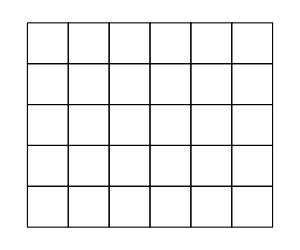

```mathematica
TessellationPlot[ConstantArray[0,{5,6}]]
```

Use a different basis for the lattice:

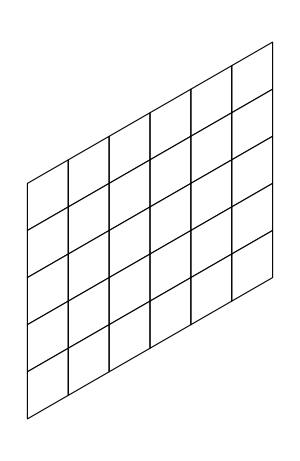

```mathematica
TessellationPlot[ConstantArray[0,{5,6}],{{Sqrt[3]/2,1/2},{0,1}}]
```

### Options

#### CellShape

By default, TessellationPlot uses parallelogrammatic cells:

```mathematica
TessellationPlot[ConstantArray[0,{5,6}]]
```

-Graphics-

Set “CellShape” to obtain different cells:

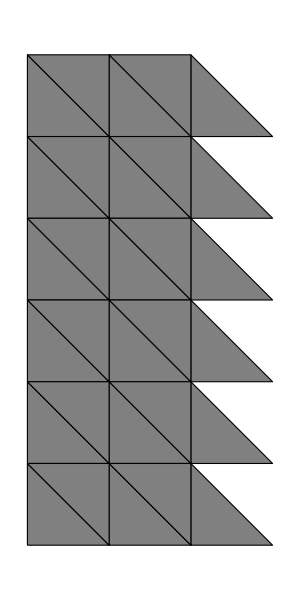

```mathematica
TessellationPlot[ConstantArray[1/2,{5,6}],"CellShape"->"Triangle"]
```

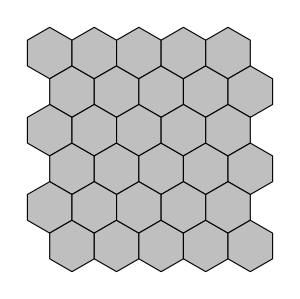

```mathematica
TessellationPlot[ConstantArray[1/4,{5,6}],{{Sqrt[3]/2,1/2},{0,1}},"CellShape"->"Hexagon"]
```

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Jack Heimrath

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Cellular Automata

Lattices

Tessellation

Graphics

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

Graphics

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

TessellationCAPlot

TessellationCAEvolution

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Weisstein, Eric W. “Cellular Automaton.” From MathWorld--A Wolfram Web Resource. http://mathworld.wolfram.com/CellularAutomaton.html

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

This function, along with the TessellationCAPlot and TessellationCAEvolution functions, are the end result of my Wolfram Summer School 2019 project. As such, it would be best if these functions were considered together.